```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
DataAsharp= Import["ASharp_strain.txt", "Data"];
DataCE  = Import["cosmic_explorer_strain.txt", "Data"];
```

### Interpolate then re-table ASDs to have even frequency spacing

```mathematica
DataInterp[data_] := Interpolation[data];
```

```mathematica
ASharpInterp = DataInterp[DataAsharp];
CEInterp = DataInterp[DataCE];
```

```mathematica
CENew = Table[{f, CEInterp[f]}, {f, Min[DataCE[[All,1]]],  Max[DataCE[[All,1]]], .03}];
```

```mathematica
ASharpNew = Table[{f, ASharpInterp[f]}, {f, Min[DataAsharp[[All,1]]],  Max[DataAsharp[[All,1]]], .03}];
```

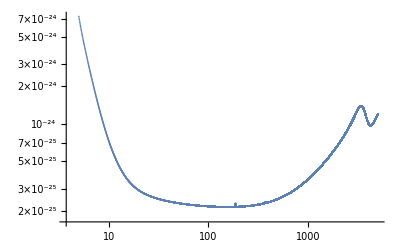

```mathematica
ListLogLogPlot[{CENew}]
```

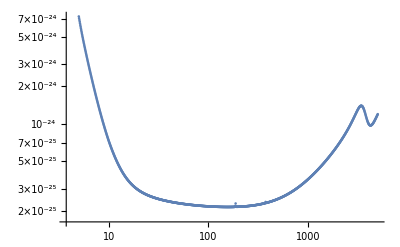

```mathematica
ListLogLogPlot[DataCE]
```

## Now define sigmas

```mathematica
Sigmas[ASD1_, ASD2_, δf_, Time_, H0_, freq_] := (1/δf) (1/Time)(10 Pi^2/(3 H0^2))^2 freq^6 ASD1^2 ASD2^2
```

```mathematica
df = 0.03;
Time  = 365.25*24*3600;
H0 = 2.193 10^(-18);
```

### Lets consider two cases: Asharp with H/L and CE with H/L

```mathematica
SigmasAsharp = Table[{ASharpNew[[i, 1]], Sqrt[Sigmas[ASharpNew[[i, 2]],ASharpNew[[i, 2]], df, Time, H0, ASharpNew[[i,1]]]]}, {i, 1,Length[ASharpNew]}];
```

```mathematica
SigmasCE = Table[{CENew[[i, 1]], Sqrt[Sigmas[CENew[[i, 2]],CENew[[i, 2]], df, Time, H0, CENew[[i,1]]]]}, {i, 1,Length[CENew]}];
```

```mathematica
ListLogLogPlot[{SigmasAsharp, SigmasCE}]
```

-Graphics-

```mathematica
Export["SigmasAsharp.txt", SigmasAsharp, "Table", "FieldSeparators" -> " "]
```

SigmasAsharp.txt

```mathematica
Export["SigmasCE.txt", SigmasCE, "Table", "FieldSeparators" -> " "]
```

SigmasCE.txt